```mathematica
NotebookSave[]
```

# Holographic Exploration Notebook

## Function definitions

The idea of the hologram centers around spherical waves that satisfy the Helmholtz equation (∇^2 + k^2)ψ = ρ(r). The Green’s function for this equation is given by 
	G(r⃗,r⃗') = e^(ⅈk|r⃗-r⃗'|)/(4π|r⃗-r⃗'|).
This Green’s function then tells us that the field at any point in space r due to a source distribution is then
	ψ(r⃗) =∫ e^(ⅈk|r⃗-r⃗'|)/(4π|r⃗-r⃗'|)ρ(r⃗')dr'^3.
For a source that is a collection of point sources, the integral then becomes a sum over the positions of these point sources.

The spherical expansion of the Green’s function
	G (r⃗, r⃗') = ik ∑_(l=0)^∞ j_l(kr_<)h_l^(1)(kr_>)∑_(m=-l)^l Y_lm(n̂)(Y^*)_lm(n̂')
	
Using this spherical expansion, the Fourier coefficients of the hologram of a point source at r⃗', recorded at a radius r is the entire factor excluding the spherical harmonic.
	f_lm (r⃗, r⃗') = ik j_l(kr_<)h_l^(1)(kr_>)(Y^*)_lm(n̂')
If we specify which of r,r’ is lesser in magnitude then the function multipoleExpansion can be used to give the Fourier coefficient 

The function fCoeff considers a point source at r⃗=(r,θ,ϕ)	and a hologram recorded at r_H and returns the fourier coefficients for this hologram.

The power of a hologram is defined to be
	P_l=1/(2l+1) ∑_(m=-l)^l |f_lm|^2.
Finally the displacement and hologram give the hologram as specified in spherical coordinates (ie. using the first expression for the Green’s function rather than the spherical expansion). These functions are used to verify the Fourir transform.

```mathematica
multipoleExpansion[r_,rLesser_,rGreater_,k_,l_,m_,theta_,phi_]:=ⅈ*k*Exp[ⅈ*k*r]*SphericalBesselJ[l,k*rLesser]*SphericalHankelH1[l,k*rGreater]*SphericalHarmonicY[l,m,theta,phi];
fCoeff[r_,rH_,k_,l_,m_,theta_,phi_]:=If[r<rH,multipoleExpansion[r,r,rH,k,l,m,theta,phi],multipoleExpansion[r,rH,r,k,l,m,theta,phi]];
power[r_,rH_,k_,l_,theta_,phi_]:=Sum[fCoeff[r,rH,k,l,m,theta,phi]*Conjugate[fCoeff[r,rH,k,l,m,theta,phi]],{m,-l,l}]/(2l+1)
```

```mathematica
displacement[r_,t_,p_,rp_,tp_,pp_]:=Sqrt[r^2+rp^2-2*r*rp*(Cos[t-tp]+Sin[t]Sin[tp](Cos[p-pp]-1))];
hologram[r_,rH_,k_,theta_,phi_,θ_,Φ_]:=Exp[ⅈ*k*r]*Exp[ⅈ*k*displacement[r,theta,phi,rH,θ,Φ]]/displacement[r,theta,phi,rH,θ,Φ];
```

## Power Analysis for Point Sources

We can plot the power P_l as we vary the position of the holographic surface r_H, the point source distance r, and the wavenumber of the radiation k.

In red is the power of the hologram due to a point source at radius r recorded over the recording surface with radius r_H. The radiation has wavenumber k. The blue power spectrum is the same power spectrum but with a damping term specified by kd.

```mathematica
rH:=5.;
Manipulate[DiscretePlot[{power[r,rH,k,l,0.,0.],power[r,rH,k+kd*ⅈ,l,0.,0.]},{l,0,20},PlotRange->All,PlotStyle->{Red,Blue}],{r,.001*rH,5.1*rH},{k,0.001*rH,5.1*rH},{kd,0.,.1*rH}]
```

Here is the same plot with the power scaled on a log-axis.

```mathematica
rH:=5.;
Manipulate[DiscretePlot[{Log[power[r,rH,k,l,0.,0.]],Log[power[r,rH,k+kd*ⅈ,l,0.,0.]]},{l,0,20},PlotRange->All,PlotStyle->{Red,Blue}],{r,.001*rH,5.1*rH},{k,0.001*rH,5.1*rH},{kd,0.,0.1*rH}]
```

Lastly here is the plot of the ratio of the damped power to the undamped power.

```mathematica
rH:=5.;
Manipulate[DiscretePlot[power[r,rH,k+kd*ⅈ,l,0.,0.]/power[r,rH,k,l,0.,0.],{l,0,20},PlotRange->All],{r,.001*rH,5.1*rH},{k,0.001*rH,5.1*rH},{kd,0.,0.1*rH}]
```

## Hologram plots

Interactive plot of the real signal of holograms and a few movies.

1. Interactive that allows for viewing at all angles. r = point source radius
2.

```mathematica
Manipulate[low=MinValue[Re[hologram[r,rH,1.,0.,0.,t,p]],{t,p}];high=MaxValue[Re[hologram[r,rH,1.,0.,0.,t,p]],{t,p}];SphericalPlot3D[1.,{θ,0,π},{Φ,0,2 π},PlotPoints->80,ColorFunction->Function[{x,y,z,θ,Φ,rl},ColorData["DarkRainbow"][Rescale[Re[hologram[r,rH,k,0.,0.,θ,Φ]],{-1,1},{-50,50}]]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->True,PlotLegends->Automatic,PlotStyle->Opacity[0.9],AxesOrigin->{0,0,0},AxesStyle->{{Thick,Red},{Thick,Green},{Thick,Blue}},ViewPoint->{2*Sin[2*Pi*r/75.],2*Sin[2*Pi*r/75.],2*Cos[2*Pi*r/75.]}],{r,0.01*rH,5.1*rH},{k,0.01*rH,5.1*rH}]
```

Interactive plot of hologram as the point source moves vertically on the z-axis at a distance from the origin r  (same as last plot) with fourier coefficients at right.

```mathematica
k:=1.;
rH:=20.;
Manipulate[low=MinValue[Re[hologram[r,rH,1.,0.,0.,t,p]],{t,p}];high=MaxValue[Re[hologram[r,rH,1.,0.,0.,t,p]],{t,p}];GraphicsRow[{SphericalPlot3D[1.,{θ,0,π},{Φ,0,2 π},PlotPoints->80,ColorFunction->Function[{x,y,z,θ,Φ,rl},ColorData["DarkRainbow"][Rescale[Re[hologram[r,rH,1.,0.,0.,θ,Φ]],{-1,1},{-50,50}]]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->True,PlotLegends->Automatic,PlotStyle->Opacity[0.9],AxesOrigin->{0,0,0},Ticks->None,AxesStyle->{{Thick,Red,Opacity[0.4]},{Thick,Green,Opacity[0.4]},{Thick,Blue,Opacity[0.4]}},ViewPoint->{2*Sin[2*Pi*r/75.+Pi/4],2*Sin[2*Pi*r/75.+Pi/4],2*Cos[2*Pi*r/75.+Pi/4]}],DiscretePlot[{power[r,rH,k,l,0.,0.]},{l,0,40},PlotRange->All]}],{r,0.01*rH,5.1*rH}]
```

Same as above plot with automatic animation,

```mathematica
Animate[k:=1.;
rH:=20.;GraphicsRow[{SphericalPlot3D[1.,{θ,0,π},{Φ,0,2 π},PlotPoints->20,ColorFunction->Function[{x,y,z,θ,Φ,rl},ColorData["DarkRainbow"][Rescale[Re[hologram[r,rH,1.,0.,0.,θ,Φ]],{-1,1},{-50,50}]]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->True,PlotLegends->Automatic,PlotStyle->Opacity[0.9],AxesOrigin->{0,0,0},Ticks->None,AxesStyle->{{Thick,Red,Opacity[0.2]},{Thick,Green,Opacity[0.2]},{Thick,Blue,Opacity[0.2]}},ViewPoint->{1.,1.,1.},ImageSize->Large],DiscretePlot[{power[r,rH,k,l,0.,0.]},{l,0,40},PlotRange->All]}],{r,1.1,40.1,1.,Appearance->"Labeled"},AnimationRate->.6]
```

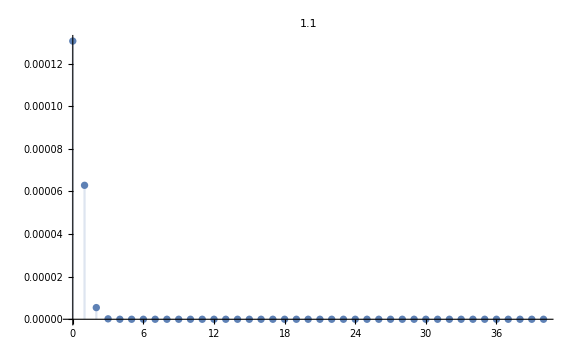
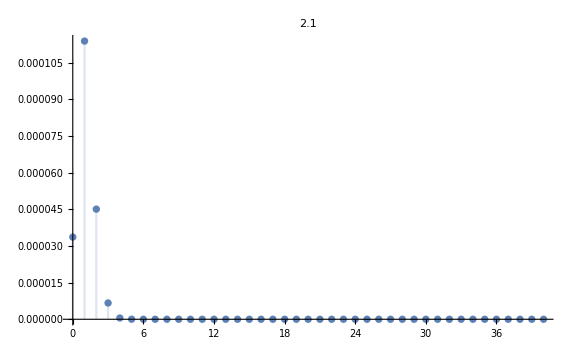
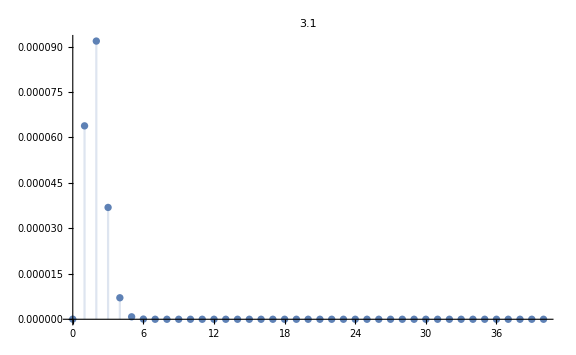
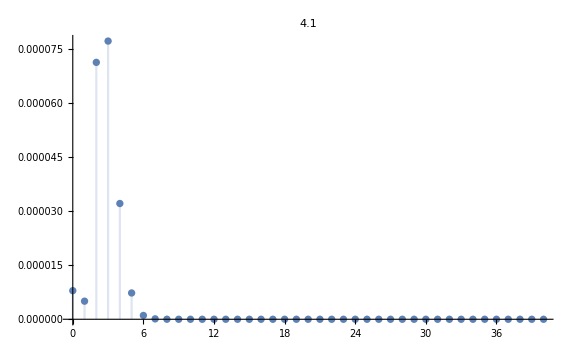
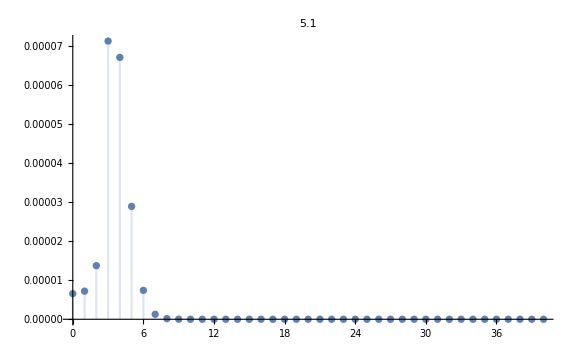
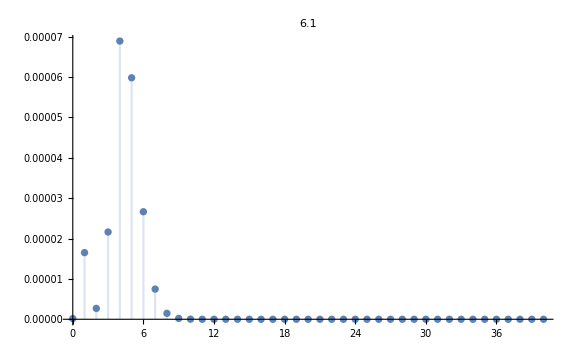
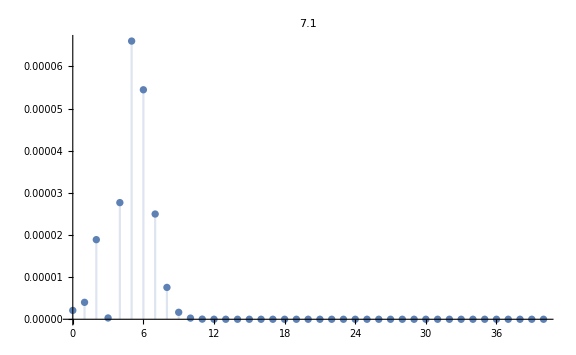
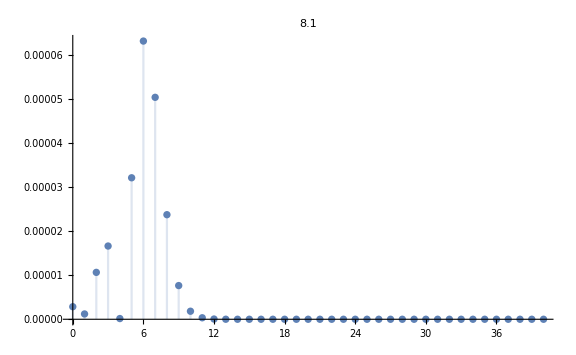

```mathematica
dat=Table[k:=1.;
rH:=20.;GraphicsRow[{SphericalPlot3D[1.,{θ,0,π},{Φ,0,2 π},PlotPoints->100,ColorFunction->Function[{x,y,z,θ,Φ,rl},ColorData["DarkRainbow"][Rescale[Re[hologram[r,rH,1.,0.,0.,θ,Φ]],{-1,1},{-50,50}]]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->True,PlotLegends->Automatic,PlotStyle->Opacity[1.0],AxesOrigin->{0,0,0},Ticks->None,AxesStyle->{{Thick,Red,Opacity[0.2]},{Thick,Green,Opacity[0.2]},{Thick,Blue,Opacity[0.2]}},ViewPoint->{1.,1.,1.},ImageSize->Large],DiscretePlot[{power[r,rH,k,l,0.,0.]},{l,0,40},PlotRange->All,ImageSize->Large,PlotLabel->r]}],{r,1.1,40.1,1.}]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/mpun/Desktop

```mathematica
Export["mov.gif",dat,"DisplayDurations"->0.7]
```

mov.gif